#### Using Euler' s Explicit method to solve the first order differential equation y' = y with y (0) = 1

```mathematica
yEuler=NDSolveValue[{y'[t]==y[t],y[0]==1},y,{t,0,5},Method->"ExplicitEuler",MaxStepFraction->1]
```

InterpolatingFunction[{{0., 5.}}, <>]

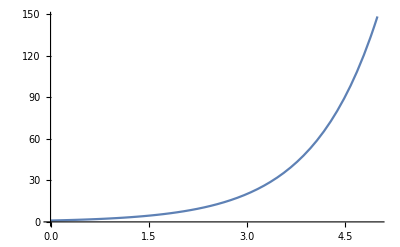

```mathematica
Plot[yEuler[t],{t,0,5}]
```

#### What is the step size automatically chosen by Mathematica and NDSolve?

The probing of the solution and technique need a special package called NDSolveUtilities to be loaded into the current instance of Mathematica.

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
```

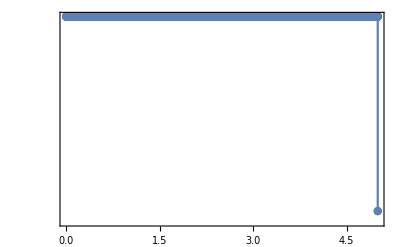

```mathematica
StepDataPlot[yEuler,PlotStyle->{Thickness[0.004]}]
```

#### Deliverable

Play with MaxStepFraction and check the step size chosen by NDSolveValue.  Create a brief 1-2 page report using LATEX to describe your observations.  Ensure that you thoroughly read the Mathematical Help Manual for information on specific switches or functions. Use the Chicago citation style to cite your sources.  Your sources may not be blogs or webpages.

Try this same problem with NDSolve instead of NDSolveValue and report any difference in function structure (for solution or visualization) in this report.